```mathematica
Clear["Global`*"];
baseURL="dev/vis/project/data";
rawDir=baseURL~StringJoin~"/raw/";
cleanedDir=baseURL~StringJoin~"/cleaned/";
data=Import[rawDir~StringJoin~"20170223.csv"]
```

{{md5,content,phone,conntime,recitime,lng,lat},144119,{7a0e71f4e235372fd77c764729740b24,尊敬的用户您好：您的信用卡已达到我行提额标准，可提升5万元，详情致电010-57435021我行将在一个工作日内完成提额调整【工商银行】
,95588,1487832377000,1487833295000,116.341,39.7527}}
 |  |  |  |

```mathematica
mainData=data⟦2;;All,2;;All⟧;
```

```mathematica
positions=GeoPosition/@mainData⟦All,{-1,-2}⟧;
```

```mathematica
MinMax/@Transpose[mainData⟦All,{-1,-2}⟧]
```

{{39.4735,40.4544},{115.754,117.259}}

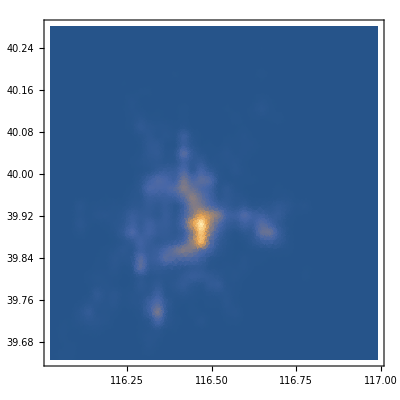

```mathematica
densPlot=SmoothDensityHistogram[mainData⟦All,{-2,-1}⟧]
```

```mathematica
GeoGraphics[{Opacity[0.6],densPlot⟦1⟧},GeoBackground->Automatic]
```

-Graphics-

```mathematica
Clear["Global`*"];
baseURL="dev/vis/project/data";
rawDir=baseURL~StringJoin~"/raw/";
cleanedDir=baseURL~StringJoin~"/cleaned/";
files=FileNames["*",rawDir];
ToDateList:=ToExpression/@{StringTake[#,4],StringTake[#,{5,6}],StringTake[#,{7,8}]}&[StringReplace[#,(__~~"/")|".csv"-> ""]]&;
InBeijingQ[lng_Real,lat_Real]:=116<lng<119&&38<lat<41;

Parallelize@Map[
Function[dataPath,
Module[{dateList,timeRange,InTimeRangeQ,data,selected,toExport},
dateList=ToDateList[dataPath];
timeRange=1000*UnixTime/@{dateList~Join~{0},dateList~Join~{24}};
InTimeRangeQ:=timeRange⟦1⟧≤#<timeRange⟦2⟧&;
data=Join[#⟦1;;3⟧,ToExpression/@#⟦4;;7⟧]&/@Import[dataPath,"CSV","Numeric"->False]⟦2;;All⟧;
Print[StringForm["File `` read.", dataPath]];
(* Select the valid data *)
selected=
Select[data,
InTimeRangeQ[#⟦4⟧]
&&InTimeRangeQ[#⟦5⟧]
&&InBeijingQ@@#⟦6;;7⟧
&&{String,String,String,Integer,Integer,Real,Real}==Head/@#&
];
Print[StringForm["File `` devided.", dataPath]];
toExport=Table[Select[selected,DateList[UnixTime[#⟦4⟧/1000]]⟦4⟧==h&],{h,0,23}];
Print[StringForm["File `` ready to export.", dataPath]];
Table[Export[FileNameJoin[{cleanedDir,TemplateApply[StringTemplate["``-``-``-``"],If[#>100,ToString[#],IntegerString[#,10,2]]&/@(dateList~Join~{i-1})]<>".json"}],toExport⟦i⟧]

,{i,Length@toExport}]
]
],files]
```

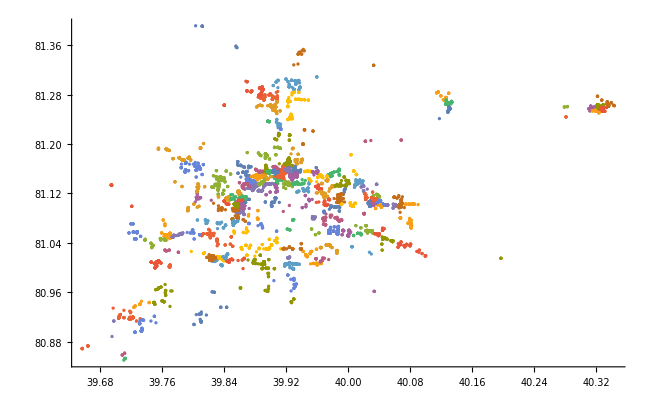

```mathematica
Clear["Global`*"];
baseURL="dev/vis/project/data";
rawDir=baseURL~StringJoin~"/raw/";
cleanedDir=baseURL~StringJoin~"/cleaned/";
files=FileNames["*",cleanedDir];
ToDateList:=ToExpression/@StringSplit[StringReplace[#,(__~~"/")|".json"-> ""],"-"]&;
data=Import[files⟦1⟧];
cosMeanLat=Mean@data⟦All,-1⟧Degree;
ListPlot[FindClusters[{#⟦-1⟧,#⟦-2⟧cosMeanLat}&/@data,200]]
```

```mathematica
Clear["Global`*"];
baseURL="dev/vis/project/data";
resultDir=FileNameJoin[{baseURL,"result"}];
exportDir=FileNameJoin[{baseURL,"others"}];
files=FileNames["*",resultDir];
ToDateList:=ToExpression/@StringSplit[StringReplace[#,(__~~"/")|".json"-> ""],"-"]&;
Parallelize@Map[Function[datePath,Module[{data,dateList,toExport},
dateList=ToDateList[datePath];
data=Import[datePath];
toExport=Select[data,#⟦-2⟧=="其他"&]⟦All,7;;8⟧;
Export[FileNameJoin[{exportDir,TemplateApply[StringTemplate["``-``-``-``"],If[#>100,ToString[#],IntegerString[#,10,2]]&/@(dateList~Join~{i-1})]<>".json"}],toExport,"Compact"->True]
]],files]
```

```mathematica
Clear["Global`*"];
baseURL="dev/vis/project/data";
rawDir=baseURL~StringJoin~"/raw/";
cleanedDir=baseURL~StringJoin~"/cleaned/";
data=Import[rawDir~StringJoin~"20170223.csv"];
```

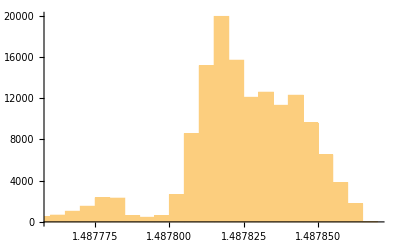

```mathematica
Histogram[Select[data⟦All,-4⟧,#>1487000000000&]]
```

```mathematica
DateList@FromUnixTime[1487836803]
```

{2017,2,23,16,0,3.}

```mathematica
DateList@FromUnixTime[1487803802]
```

{2017,2,23,6,50,2.}

```mathematica
Clear["Global`*"];
baseDir="dev/vis/project/bs-vis/api/loc/scam";
files=FileNames["*",baseDir];
ToCorrect[s_String]:=IntegerString[If[ToExpression[s]<8,ToExpression[s]+16,ToExpression[s]-8],10,2];
RenameToTemp[filename_String]:={filename,StringReplace[filename,"-"~~x:DigitCharacter..~~"."-> "-"<>ToCorrect[x]<>".new."]}
Apply[RenameFile,RenameToTemp/@files,{1}]
```

```mathematica
Clear["Global`*"];
baseDir="dev/vis/project/bs-vis/api/loc/scam";
files=FileNames["*",baseDir];RenameToResult[filename_String]:={filename,StringReplace[filename,".new"->"" ]};
Apply[RenameFile,RenameToResult/@files,{1}]
```